#### Качественный анализ модели Самуэльсона-Хикса

```mathematica
G = {u,
-(1-r)u-(1-c)y+a};
```

```mathematica
points=Solve[G==0,{y,u}]
```

{{y→-a/(-1+c),u→0}}

```mathematica
A=Grad[G,{y,u}];
A //MatrixForm
```

(0 | 1
-1+c | -1+r)

```mathematica
det=Det@A
```

1-c

```mathematica
trace=Tr@A
```

-1+r

```mathematica
trace^2-4det
```

-4 (1-c)+(-1+r)^2

Фазовый портрет:
  - центр при , 
		- устойчивый узел при  &  ,
		- неустойчивый узел при ,
		- устойчивый фокус при ,
		- неустойчивый фокус при

```mathematica
streamPlot[G_List,points_List,params_List,{umin_,umax_},arrowSize_Real]:=Module[
{ymax},
ymax =Round@points⟦1,1,2⟧/.params;
StreamPlot[G/.params,
{y,0,2ymax},{u,umin,umax},
Epilog->{Red,Point[(points/.params)⟦All,All,2⟧]},
StreamPoints->Fine,
StreamScale->{Full, All, arrowSize},
StreamColorFunction->"Rainbow",
PerformanceGoal->"Quality"]
]
```

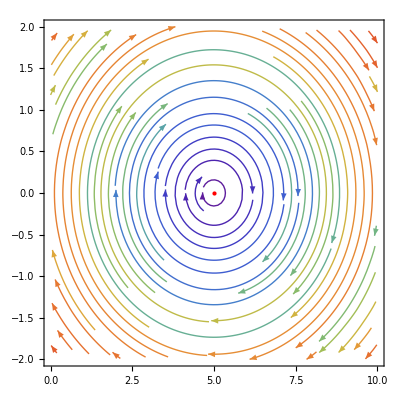

```mathematica
streamPlot[G,points,{c->0.8,r->1,a->1},{-2,2},.015]
```

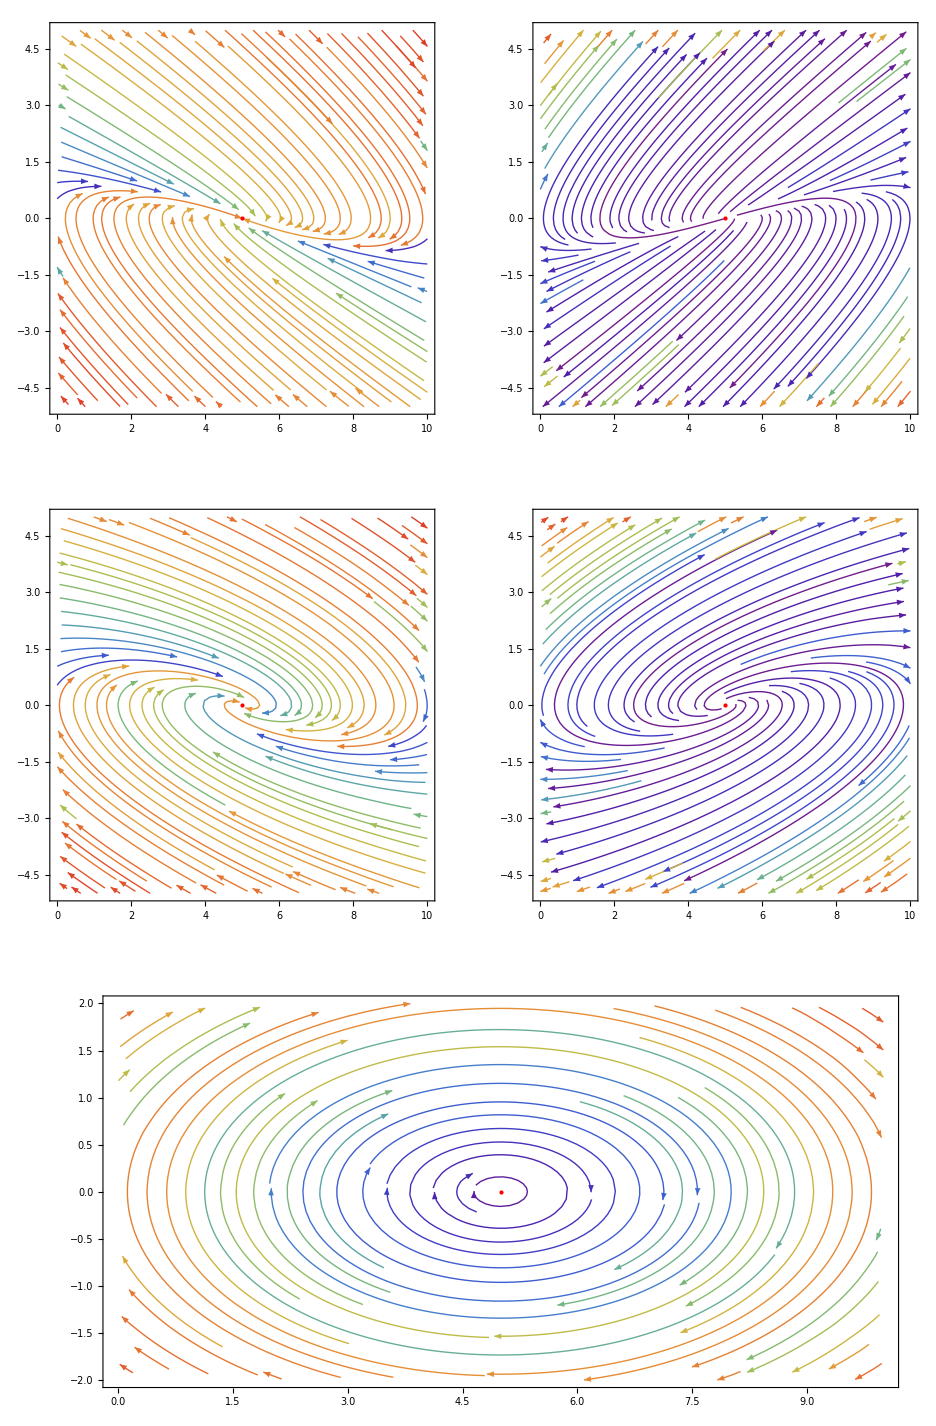

```mathematica
GraphicsGrid[
{
{streamPlot[G,points,{c->0.8,r->0.1,a->1},{-5,5},.015],
streamPlot[G,points,{c->0.8,r->2,a->1},{-5,5},.015]},

{streamPlot[G,points,{c->0.8,r->0.5,a->1},{-5,5},.015],
streamPlot[G,points,{c->0.8,r->1.5,a->1},{-5,5},.015]},

{streamPlot[G,points,{c->0.8,r->1,a->1},{-2,2},.015],
SpanFromLeft}
}
]
```